```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[X_] := X^RandomReal[{0,2}]
```

```mathematica
data1 = Table[f[i],{i,1,10,1}];
```

```mathematica
<<data_Intro_PS_overfit;
```

```mathematica
lineSimple=Fit[data,{1,x},x]
```

2.85487+1.0263 x

```mathematica
lineComplex=Fit[data,{1,x,x^2,x^3,x^4,x^5},x]
```

-8.66977+20.879 x-15.0308 x^2+4.46158 x^3-0.53011 x^4+0.0214794 x^5

```mathematica
lineComplex[1]
```

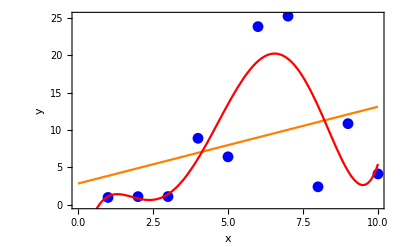

```mathematica
gPlain=Show[ListPlot[data,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"x","y"}],Plot[lineSimple,{x,0,10},PlotStyle->Orange],Plot[lineComplex,{x,0,10},PlotStyle->Red]]
```

```mathematica
Export["Intro_PS_overfitUnmarked.pdf",gPlain]
```

Intro_PS_overfitUnmarked.pdf

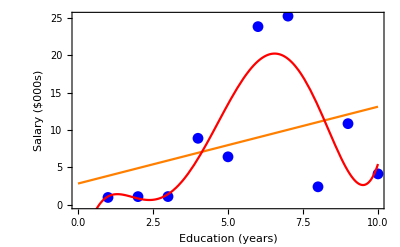

```mathematica
Show[ListPlot[data,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"Education (years)","Salary ($000s)"}],Plot[lineSimple,{x,0,10},PlotStyle->Orange],Plot[lineComplex,{x,0,10},PlotStyle->Red]]
```

## Generating a large data file with data from the model

```mathematica
data1=Table[Table[f[i],{i,1,10,1}],{100}];
```

```mathematica
fSumSquareResiduals[aLine_,lData_]:= Module[{lDataSim = Table[aLine/.{x->i},{i,1,10,1}],lResiduals},lResiduals=lData-lDataSim; Total[#^2&/@lResiduals]]
```

```mathematica
Mean@(fSumSquareResiduals[lineComplex,#]&/@data1)
```

2174.61

```mathematica
Mean@(fSumSquareResiduals[lineSimple,#]&/@data1)
```

1624.95

```mathematica
Export["Intro_PS_overfitLong.csv",data2]
```

Intro_PS_overfitLong.csv

```mathematica
Export["Intro_PS_overfitShort.csv",data]
```

Intro_PS_overfitShort.csv